```mathematica
width = 41;
height =41;
xs=(width+1)/2;
ys=(height+1)/2;

dx = 0.01;
dy = 0.01;
As = 1.0*^-5;
η=0.01;(*0.01*)(*0.00001 not increasing*)
grid=Table[{i*dx,j*dy},{i,1,width},{j,1,height}];
ghostarray=Table[0.0,width+2,height+2];
ghostarray=Table[0.0,width+2,height+2];
laplacian[array_]:={
lparray=array;
ghostarray⟦2;;-2,2;;-2⟧=array⟦;;,;;⟧;
ghostarray⟦2;;-2,1⟧ = array⟦;;,1⟧;
ghostarray⟦2;;-2,-1⟧ = array⟦;;,-1⟧;
ghostarray⟦1,2;;-2⟧ = array⟦1,;;⟧;
ghostarray⟦-1,2;;-2⟧ = array⟦-1,;;⟧;
lparray⟦;;,;;⟧=(ghostarray⟦3;;-1,2;;-2⟧+ghostarray⟦1;;-3,2;;-2⟧-2ghostarray⟦2;;-2,2;;-2⟧)/dx^2+(ghostarray⟦2;;-2,3;;-1⟧+ghostarray⟦2;;-2,1;;-3⟧-2ghostarray⟦2;;-2,2;;-2⟧)/dy^2;
lparray
}⟦1⟧

ghostarray1=Table[0.0,width+2,height+2];
ghostarray2=Table[0.0,width+2,height+2];
gradgrad[array1_,array2_]:={
ggarray=array1;
ghostarray1⟦2;;-2,2;;-2⟧=array1⟦;;,;;⟧;
ghostarray2⟦2;;-2,2;;-2⟧=array2⟦;;,;;⟧;
ghostarray1⟦2;;-2,1⟧ = array1⟦;;,1⟧;
ghostarray1⟦2;;-2,-1⟧ = array1⟦;;,-1⟧;
ghostarray1⟦1,2;;-2⟧ = array1⟦1,;;⟧;
ghostarray1⟦-1,2;;-2⟧ = array1⟦-1,;;⟧;
ghostarray2⟦2;;-2,1⟧ = array2⟦;;,1⟧;
ghostarray2⟦2;;-2,-1⟧ = array2⟦;;,-1⟧;
ghostarray2⟦1,2;;-2⟧ = array2⟦1,;;⟧;
ghostarray2⟦-1,2;;-2⟧ = array2⟦-1,;;⟧;
ggarray⟦;;,;;⟧=1/(4 dx^2)(ghostarray1⟦3;;-1,2;;-2⟧-ghostarray1⟦1;;-3,2;;-2⟧)(ghostarray2⟦3;;-1,2;;-2⟧-ghostarray2⟦1;;-3,2;;-2⟧)+1/(4 dy^2)(ghostarray1⟦2;;-2,3;;-1⟧-ghostarray1⟦2;;-2,1;;-3⟧)(ghostarray2⟦2;;-2,3;;-1⟧-ghostarray2⟦2;;-2,1;;-3⟧);
ggarray
}⟦1⟧

laplacianS[array_]:={
lparray=array;
ghostarray⟦2;;-2,2;;-2⟧=array⟦;;,;;⟧;
ghostarray⟦2;;-2,1⟧ = array⟦;;,1⟧;
ghostarray⟦2;;-2,-1⟧ = array⟦;;,-1⟧;
ghostarray⟦1,2;;-2⟧ = array⟦1,;;⟧;
ghostarray⟦-1,2;;-2⟧ = array⟦-1,;;⟧;
lparray⟦;;,;;⟧=(ghostarray⟦3;;-1,2;;-2⟧+ghostarray⟦1;;-3,2;;-2⟧-2ghostarray⟦2;;-2,2;;-2⟧)/dx^2+(ghostarray⟦2;;-2,3;;-1⟧+ghostarray⟦2;;-2,1;;-3⟧-2ghostarray⟦2;;-2,2;;-2⟧)/dy^2;
lparray⟦xs,ys⟧=η*lparray⟦xs,ys⟧;
lparray⟦xs+1,ys⟧=((ghostarray⟦xs+3,ys+1⟧-ghostarray⟦xs+2,ys+1⟧)-η(ghostarray⟦xs+2,ys+1⟧-ghostarray⟦xs+1,ys+1⟧))/dx^2+((ghostarray⟦xs+2,ys+3⟧-ghostarray⟦xs+2,ys+2⟧)-(ghostarray⟦xs+2,ys+2⟧-ghostarray⟦xs+2,ys+1⟧))/dy^2;
lparray⟦xs-1,ys⟧=(η(ghostarray⟦xs+1,ys+1⟧-ghostarray⟦xs,ys+1⟧)-(ghostarray⟦xs,ys+1⟧-ghostarray⟦xs-1,ys+1⟧))/dx^2+((ghostarray⟦xs,ys+2⟧-ghostarray⟦xs,ys+1⟧)-(ghostarray⟦xs,ys+1⟧-ghostarray⟦xs,ys⟧))/dy^2;
lparray⟦xs,ys+1⟧=((ghostarray⟦xs+2,ys+2⟧-ghostarray⟦xs+1,ys+2⟧)-(ghostarray⟦xs+1,ys+2⟧-ghostarray⟦xs,ys+2⟧))/dx^2+((ghostarray⟦xs+1,ys+3⟧-ghostarray⟦xs+1,ys+2⟧)-η(ghostarray⟦xs+1,ys+2⟧-ghostarray⟦xs+1,ys+1⟧))/dy^2;
lparray⟦xs,ys-1⟧=((ghostarray⟦xs+2,ys⟧-ghostarray⟦xs+1,ys⟧)-(ghostarray⟦xs+1,ys⟧-ghostarray⟦xs,ys⟧))/dx^2+(η(ghostarray⟦xs+1,ys+1⟧-ghostarray⟦xs+1,ys⟧)-(ghostarray⟦xs+1,ys⟧-ghostarray⟦xs+1,ys-1⟧))/dy^2;
lparray
}⟦1⟧
ghostarray1=Table[0.0,width+2,height+2];
ghostarray2=Table[0.0,width+2,height+2];
gradgradS[array1_,array2_]:={
ggarray=array1;
ghostarray1⟦2;;-2,2;;-2⟧=array1⟦;;,;;⟧;
ghostarray2⟦2;;-2,2;;-2⟧=array2⟦;;,;;⟧;
ghostarray1⟦2;;-2,1⟧ = array1⟦;;,1⟧;
ghostarray1⟦2;;-2,-1⟧ = array1⟦;;,-1⟧;
ghostarray1⟦1,2;;-2⟧ = array1⟦1,;;⟧;
ghostarray1⟦-1,2;;-2⟧ = array1⟦-1,;;⟧;
ghostarray2⟦2;;-2,1⟧ = array2⟦;;,1⟧;
ghostarray2⟦2;;-2,-1⟧ = array2⟦;;,-1⟧;
ghostarray2⟦1,2;;-2⟧ = array2⟦1,;;⟧;
ghostarray2⟦-1,2;;-2⟧ = array2⟦-1,;;⟧;
ggarray⟦;;,;;⟧=1/(4 dx^2)(ghostarray1⟦3;;-1,2;;-2⟧-ghostarray1⟦1;;-3,2;;-2⟧)(ghostarray2⟦3;;-1,2;;-2⟧-ghostarray2⟦1;;-3,2;;-2⟧)+1/(4 dy^2)(ghostarray1⟦2;;-2,3;;-1⟧-ghostarray1⟦2;;-2,1;;-3⟧)(ghostarray2⟦2;;-2,3;;-1⟧-ghostarray2⟦2;;-2,1;;-3⟧);
ggarray⟦xs,ys⟧=η ggarray⟦xs,ys⟧;

ggarray⟦xs+1,ys⟧=1/(4 dx^2)((ghostarray1⟦xs+3,ys+1⟧-ghostarray1⟦xs+2,ys+1⟧)+η(ghostarray1⟦xs+2,ys+1⟧-ghostarray1⟦xs+1,ys+1⟧))((ghostarray2⟦xs+3,ys+1⟧-ghostarray2⟦xs+2,ys+1⟧)+η(ghostarray2⟦xs+2,ys+1⟧-ghostarray2⟦xs+1,ys+1⟧))+1/(4 dy^2)((ghostarray1⟦xs+2,ys+3⟧-ghostarray1⟦xs+2,ys+2⟧)+(ghostarray1⟦xs+2,ys+2⟧-ghostarray1⟦xs+2,ys+1⟧))((ghostarray2⟦xs+2,ys+3⟧-ghostarray2⟦xs+2,ys+2⟧)+(ghostarray2⟦xs+2,ys+2⟧-ghostarray2⟦xs+2,ys+1⟧));


ggarray⟦xs-1,ys⟧=1/(4 dx^2)(η(ghostarray1⟦xs+1,ys+1⟧-ghostarray1⟦xs,ys+1⟧)+(ghostarray1⟦xs,ys+1⟧-ghostarray1⟦xs-1,ys+1⟧))(η(ghostarray2⟦xs+1,ys+1⟧-ghostarray2⟦xs,ys+1⟧)+(ghostarray2⟦xs,ys+1⟧-ghostarray2⟦xs-1,ys+1⟧))+1/(4 dy^2)((ghostarray1⟦xs,ys+2⟧-ghostarray1⟦xs,ys+1⟧)+(ghostarray1⟦xs,ys+1⟧-ghostarray1⟦xs,ys⟧))((ghostarray2⟦xs,ys+2⟧-ghostarray2⟦xs,ys+1⟧)+(ghostarray2⟦xs,ys+1⟧-ghostarray2⟦xs,ys⟧));



ggarray⟦xs,ys+1⟧=1/(4 dx^2)((ghostarray1⟦xs+2,ys+2⟧-ghostarray1⟦xs+1,ys+2⟧)+(ghostarray1⟦xs+1,ys+2⟧-ghostarray1⟦xs,ys+2⟧))((ghostarray2⟦xs+2,ys+2⟧-ghostarray2⟦xs+1,ys+2⟧)+(ghostarray2⟦xs+1,ys+2⟧-ghostarray2⟦xs,ys+2⟧))+1/(4 dy^2)((ghostarray1⟦xs+1,ys+3⟧-ghostarray1⟦xs+1,ys+2⟧)+η(ghostarray1⟦xs+1,ys+2⟧-ghostarray1⟦xs+1,ys+1⟧))((ghostarray2⟦xs+1,ys+3⟧-ghostarray2⟦xs+1,ys+2⟧)+η(ghostarray2⟦xs+1,ys+2⟧-ghostarray2⟦xs+1,ys+1⟧));


ggarray⟦xs,ys-1⟧=1/(4 dx^2)((ghostarray1⟦xs+2,ys⟧-ghostarray1⟦xs+1,ys⟧)+(ghostarray1⟦xs+1,ys⟧-ghostarray1⟦xs,ys⟧))((ghostarray2⟦xs+2,ys⟧-ghostarray2⟦xs+1,ys⟧)+(ghostarray2⟦xs+1,ys⟧-ghostarray2⟦xs,ys⟧))+1/(4 dy^2)(η(ghostarray1⟦xs+1,ys+1⟧-ghostarray1⟦xs+1,ys⟧)+(ghostarray1⟦xs+1,ys⟧-ghostarray1⟦xs+1,ys-1⟧))(η(ghostarray2⟦xs+1,ys+1⟧-ghostarray2⟦xs+1,ys⟧)+(ghostarray2⟦xs+1,ys⟧-ghostarray2⟦xs+1,ys-1⟧));

ggarray
}⟦1⟧
```

```mathematica
(*variables*)
Db = 0.1;
Dc = 0.1;
Df = 0.1;
k=10.0;
α=0.1;
β=0.1;
γ=0.1;
b0=0.01;
c0=0.0;
f0=0.001;
b0grid= Table[b0,{i,1,width},{j,1,height}];
c0grid=Table[c0,{i,1,width},{j,1,height}];
f0grid=Table[f0,{i,1,width},{j,1,height}];

tstep=7000;
dt=0.0001;
bgrid= Table[0.0,{t,1,tstep},{i,1,width},{j,1,height}];
cgrid=Table[0.0,{t,1,tstep},{i,1,width},{j,1,height}];
fgrid=Table[0.0,{t,1,tstep},{i,1,width},{j,1,height}];
bgrid⟦1⟧=b0grid;
cgrid⟦1⟧=c0grid;
fgrid⟦1⟧=f0grid;
bmax=1000*b0;
bgrid[[1,11,11]] = 1000*b0;
bgrid[[1,31,11]] = 1000*b0;
bgrid[[1,31,31]] = 1000*b0;
bgrid[[1,11,31]] = 1000*b0;
(*db = Db*laplacian[b]-k*(gradgrad[b,c]+b*laplacian[c])+α b;*)
dbt[barray_,carray_,farray_] := Db*laplacianS[barray]-k(gradgradS[barray,carray]+barray laplacianS[carray])+α barray;
dct[barray_,carray_,farray_] := Dc*laplacian[carray] +β barray farray;
dft[barray_,carray_,farray_] := Df*laplacian[farray]-γ barray;
ArrayPlot[bgrid⟦1⟧-b0grid,ColorFunction->GrayLevel,Mesh->True]
ArrayPlot[fgrid⟦1⟧-f0grid,ColorFunction->GrayLevel,Mesh->True]
```

-Graphics-

-Graphics-

```mathematica
tempcount=0;
For[i=1,i<tstep,i++,

tempcount=tempcount+1;
If[tempcount>tstep/100,
tempcount=0;
NotebookDelete[tempprint];
tempprint=PrintTemporary["Process: ",N[i/tstep*100,3]," %"];
];
bk1=dbt[bgrid⟦i⟧,cgrid⟦i⟧,fgrid⟦i⟧];
ck1=dct[bgrid⟦i⟧,cgrid⟦i⟧,fgrid⟦i⟧];
fk1=dft[bgrid⟦i⟧,cgrid⟦i⟧,fgrid⟦i⟧];

bk2=dbt[bgrid⟦i⟧+dt/2 bk1,cgrid⟦i⟧+dt/2 ck1,fgrid⟦i⟧+dt/2 fk1];
ck2=dct[bgrid⟦i⟧+dt/2 bk1,cgrid⟦i⟧+dt/2 ck1,fgrid⟦i⟧+dt/2 fk1];
fk2=dft[bgrid⟦i⟧+dt/2 bk1,cgrid⟦i⟧+dt/2 ck1,fgrid⟦i⟧+dt/2 fk1];

bk3=dbt[bgrid⟦i⟧+dt/2 bk2,cgrid⟦i⟧+dt/2 ck2,fgrid⟦i⟧+dt/2 fk2];
ck3=dct[bgrid⟦i⟧+dt/2 bk2,cgrid⟦i⟧+dt/2 ck2,fgrid⟦i⟧+dt/2 fk2];
fk3=dft[bgrid⟦i⟧+dt/2 bk2,cgrid⟦i⟧+dt/2 ck2,fgrid⟦i⟧+dt/2 fk2];

bk4=dbt[bgrid⟦i⟧+dt bk3,cgrid⟦i⟧+dt ck3,fgrid⟦i⟧+dt fk3];
ck4=dct[bgrid⟦i⟧+dt bk3,cgrid⟦i⟧+dt ck3,fgrid⟦i⟧+dt fk3];
fk4=dft[bgrid⟦i⟧+dt bk3,cgrid⟦i⟧+dt ck3,fgrid⟦i⟧+dt fk3];

bgrid⟦i+1⟧=bgrid⟦i⟧+dt/6(bk1+2bk2+2bk3+bk4);
cgrid⟦i+1⟧=cgrid⟦i⟧+dt/6(ck1+2ck2+2ck3+ck4);
fgrid⟦i+1⟧=fgrid⟦i⟧+dt/6(fk1+2fk2+2fk3+fk4)
]
```

```mathematica
Indexarray = IntegerPart[Table[i,{i,1,tstep,tstep/100}]];
bmaxval=1.1*Max[bgrid⟦#⟧-b0grid&/@Range[1,tstep,tstep/100]];
fmaxval=f0*1.1;
{ListAnimate[ArrayPlot[bgrid⟦#⟧-b0grid,ColorFunction->(Blend[{Black,White},#]&),PlotRange->{0,bmaxval},Mesh->True]&/@Indexarray],
ListAnimate[ArrayPlot[bgrid⟦#⟧-b0grid,ColorFunction->GrayLevel,Mesh->True]&/@Indexarray]}
{ListAnimate[ArrayPlot[fgrid⟦#⟧-f0grid,ColorFunction->(Blend[{Black,White},#]&),PlotRange->{0,fmaxval},Mesh->True]&/@Indexarray],
ListAnimate[ArrayPlot[fgrid⟦#⟧-f0grid,ColorFunction->GrayLevel,Mesh->True]&/@Indexarray]}
```

{,}

{,}

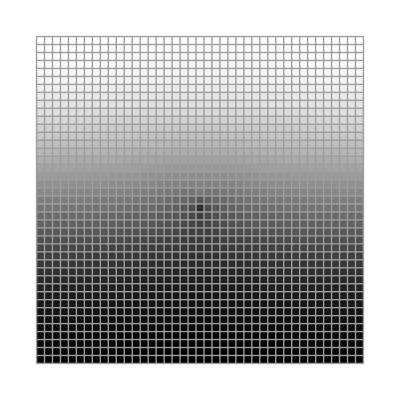

{{7.21129×10^-8,7.21117×10^-8,7.21093×10^-8,7.21059×10^-8,7.21014×10^-8,7.2096×10^-8,7.20897×10^-8,7.20828×10^-8,7.20753×10^-8,7.20675×10^-8,7.20595×10^-8,7.20514×10^-8,7.20436×10^-8,7.20361×10^-8,7.20292×10^-8,7.2023×10^-8,7.20177×10^-8,7.20135×10^-8,7.20103×10^-8,7.20084×10^-8,7.20078×10^-8,7.20084×10^-8,7.20103×10^-8,7.20135×10^-8,7.20177×10^-8,7.2023×10^-8,7.20292×10^-8,7.20361×10^-8,7.20436×10^-8,7.20514×10^-8,7.20595×10^-8,7.20675×10^-8,7.20753×10^-8,7.20828×10^-8,7.20897×10^-8,7.2096×10^-8,7.21014×10^-8,7.21059×10^-8,7.21093×10^-8,7.21117×10^-8,7.21129×10^-8},{7.20839×10^-8,7.20827×10^-8,7.20803×10^-8,7.20768×10^-8,7.20722×10^-8,7.20667×10^-8,7.20604×10^-8,7.20533×10^-8,7.20457×10^-8,7.20378×10^-8,7.20296×10^-8,7.20214×10^-8,7.20134×10^-8,7.20058×10^-8,7.19988×10^-8,7.19925×10^-8,7.19871×10^-8,7.19827×10^-8,7.19795×10^-8,7.19776×10^-8,7.19769×10^-8,7.19776×10^-8,7.19795×10^-8,7.19827×10^-8,7.19871×10^-8,7.19925×10^-8,7.19988×10^-8,7.20058×10^-8,7.20134×10^-8,7.20214×10^-8,7.20296×10^-8,7.20378×10^-8,7.20457×10^-8,7.20533×10^-8,7.20604×10^-8,7.20667×10^-8,7.20722×10^-8,7.20768×10^-8,7.20803×10^-8,7.20827×10^-8,7.20839×10^-8},{7.2026×10^-8,7.20248×10^-8,7.20223×10^-8,7.20187×10^-8,7.20141×10^-8,7.20084×10^-8,7.20018×10^-8,7.19946×10^-8,7.19867×10^-8,7.19785×10^-8,7.197×10^-8,7.19615×10^-8,7.19532×10^-8,7.19453×10^-8,7.1938×10^-8,7.19315×10^-8,7.19259×10^-8,7.19214×10^-8,7.1918×10^-8,7.1916×10^-8,7.19153×10^-8,7.1916×10^-8,7.1918×10^-8,7.19214×10^-8,7.19259×10^-8,7.19315×10^-8,7.1938×10^-8,7.19453×10^-8,7.19532×10^-8,7.19615×10^-8,7.197×10^-8,7.19785×10^-8,7.19867×10^-8,7.19946×10^-8,7.20018×10^-8,7.20084×10^-8,7.20141×10^-8,7.20187×10^-8,7.20223×10^-8,7.20248×10^-8,7.2026×10^-8},{7.19397×10^-8,7.19385×10^-8,7.19359×10^-8,7.19321×10^-8,7.19272×10^-8,7.19213×10^-8,7.19145×10^-8,7.19068×10^-8,7.18986×10^-8,7.18899×10^-8,7.18811×10^-8,7.18721×10^-8,7.18634×10^-8,7.18551×10^-8,7.18474×10^-8,7.18404×10^-8,7.18345×10^-8,7.18297×10^-8,7.18262×10^-8,7.1824×10^-8,7.18233×10^-8,7.1824×10^-8,7.18262×10^-8,7.18297×10^-8,7.18345×10^-8,7.18404×10^-8,7.18474×10^-8,7.18551×10^-8,7.18634×10^-8,7.18721×10^-8,7.18811×10^-8,7.18899×10^-8,7.18986×10^-8,7.19068×10^-8,7.19145×10^-8,7.19213×10^-8,7.19272×10^-8,7.19321×10^-8,7.19359×10^-8,7.19385×10^-8,7.19397×10^-8},{7.18256×10^-8,7.18242×10^-8,7.18215×10^-8,7.18175×10^-8,7.18123×10^-8,7.18061×10^-8,7.17988×10^-8,7.17907×10^-8,7.1782×10^-8,7.17728×10^-8,7.17633×10^-8,7.17538×10^-8,7.17444×10^-8,7.17355×10^-8,7.17272×10^-8,7.17198×10^-8,7.17134×10^-8,7.17082×10^-8,7.17044×10^-8,7.17021×10^-8,7.17013×10^-8,7.17021×10^-8,7.17044×10^-8,7.17082×10^-8,7.17134×10^-8,7.17198×10^-8,7.17272×10^-8,7.17355×10^-8,7.17444×10^-8,7.17538×10^-8,7.17633×10^-8,7.17728×10^-8,7.1782×10^-8,7.17907×10^-8,7.17988×10^-8,7.18061×10^-8,7.18123×10^-8,7.18175×10^-8,7.18215×10^-8,7.18242×10^-8,7.18256×10^-8},{7.16842×10^-8,7.16827×10^-8,7.16799×10^-8,7.16756×10^-8,7.16701×10^-8,7.16634×10^-8,7.16556×10^-8,7.16469×10^-8,7.16375×10^-8,7.16276×10^-8,7.16174×10^-8,7.16071×10^-8,7.1597×10^-8,7.15873×10^-8,7.15782×10^-8,7.15701×10^-8,7.15631×10^-8,7.15575×10^-8,7.15533×10^-8,7.15508×10^-8,7.15499×10^-8,7.15508×10^-8,7.15533×10^-8,7.15575×10^-8,7.15631×10^-8,7.15701×10^-8,7.15782×10^-8,7.15873×10^-8,7.1597×10^-8,7.16071×10^-8,7.16174×10^-8,7.16276×10^-8,7.16375×10^-8,7.16469×10^-8,7.16556×10^-8,7.16634×10^-8,7.16701×10^-8,7.16756×10^-8,7.16799×10^-8,7.16827×10^-8,7.16842×10^-8},{7.15166×10^-8,7.1515×10^-8,7.15119×10^-8,7.15073×10^-8,7.15014×10^-8,7.14941×10^-8,7.14857×10^-8,7.14764×10^-8,7.14662×10^-8,7.14554×10^-8,7.14442×10^-8,7.1433×10^-8,7.14219×10^-8,7.14112×10^-8,7.14013×10^-8,7.13923×10^-8,7.13846×10^-8,7.13783×10^-8,7.13737×10^-8,7.13708×10^-8,7.13699×10^-8,7.13708×10^-8,7.13737×10^-8,7.13783×10^-8,7.13846×10^-8,7.13923×10^-8,7.14013×10^-8,7.14112×10^-8,7.14219×10^-8,7.1433×10^-8,7.14442×10^-8,7.14554×10^-8,7.14662×10^-8,7.14764×10^-8,7.14857×10^-8,7.14941×10^-8,7.15014×10^-8,7.15073×10^-8,7.15119×10^-8,7.1515×10^-8,7.15166×10^-8},{7.13237×10^-8,7.1322×10^-8,7.13187×10^-8,7.13138×10^-8,7.13073×10^-8,7.12994×10^-8,7.12903×10^-8,7.12801×10^-8,7.12689×10^-8,7.12571×10^-8,7.12448×10^-8,7.12324×10^-8,7.12201×10^-8,7.12083×10^-8,7.11972×10^-8,7.11872×10^-8,7.11785×10^-8,7.11715×10^-8,7.11663×10^-8,7.11631×10^-8,7.1162×10^-8,7.11631×10^-8,7.11663×10^-8,7.11715×10^-8,7.11785×10^-8,7.11872×10^-8,7.11972×10^-8,7.12083×10^-8,7.12201×10^-8,7.12324×10^-8,7.12448×10^-8,7.12571×10^-8,7.12689×10^-8,7.12801×10^-8,7.12903×10^-8,7.12994×10^-8,7.13073×10^-8,7.13138×10^-8,7.13187×10^-8,7.1322×10^-8,7.13237×10^-8},{7.11069×10^-8,7.11051×10^-8,7.11015×10^-8,7.10961×10^-8,7.10891×10^-8,7.10805×10^-8,7.10705×10^-8,7.10593×10^-8,7.1047×10^-8,7.1034×10^-8,7.10204×10^-8,7.10066×10^-8,7.09929×10^-8,7.09796×10^-8,7.09671×10^-8,7.09558×10^-8,7.0946×10^-8,7.0938×10^-8,7.09321×10^-8,7.09285×10^-8,7.09273×10^-8,7.09285×10^-8,7.09321×10^-8,7.0938×10^-8,7.0946×10^-8,7.09558×10^-8,7.09671×10^-8,7.09796×10^-8,7.09929×10^-8,7.10066×10^-8,7.10204×10^-8,7.1034×10^-8,7.1047×10^-8,7.10593×10^-8,7.10705×10^-8,7.10805×10^-8,7.10891×10^-8,7.10961×10^-8,7.11015×10^-8,7.11051×10^-8,7.11069×10^-8},{7.08676×10^-8,7.08656×10^-8,7.08616×10^-8,7.08558×10^-8,7.08481×10^-8,7.08387×10^-8,7.08277×10^-8,7.08154×10^-8,7.08019×10^-8,7.07874×10^-8,7.07723×10^-8,7.07568×10^-8,7.07414×10^-8,7.07265×10^-8,7.07123×10^-8,7.06995×10^-8,7.06882×10^-8,7.06791×10^-8,7.06723×10^-8,7.06681×10^-8,7.06667×10^-8,7.06681×10^-8,7.06723×10^-8,7.06791×10^-8,7.06882×10^-8,7.06995×10^-8,7.07123×10^-8,7.07265×10^-8,7.07414×10^-8,7.07568×10^-8,7.07723×10^-8,7.07874×10^-8,7.08019×10^-8,7.08154×10^-8,7.08277×10^-8,7.08387×10^-8,7.08481×10^-8,7.08558×10^-8,7.08616×10^-8,7.08656×10^-8,7.08676×10^-8},{7.06072×10^-8,7.0605×10^-8,7.06007×10^-8,7.05943×10^-8,7.05859×10^-8,7.05756×10^-8,7.05636×10^-8,7.055×10^-8,7.0535×10^-8,7.05189×10^-8,7.0502×10^-8,7.04847×10^-8,7.04673×10^-8,7.04503×10^-8,7.04341×10^-8,7.04194×10^-8,7.04064×10^-8,7.03958×10^-8,7.0388×10^-8,7.03831×10^-8,7.03815×10^-8,7.03831×10^-8,7.0388×10^-8,7.03958×10^-8,7.04064×10^-8,7.04194×10^-8,7.04341×10^-8,7.04503×10^-8,7.04673×10^-8,7.04847×10^-8,7.0502×10^-8,7.05189×10^-8,7.0535×10^-8,7.055×10^-8,7.05636×10^-8,7.05756×10^-8,7.05859×10^-8,7.05943×10^-8,7.06007×10^-8,7.0605×10^-8,7.06072×10^-8},{7.03274×10^-8,7.03251×10^-8,7.03204×10^-8,7.03134×10^-8,7.03043×10^-8,7.0293×10^-8,7.02797×10^-8,7.02647×10^-8,7.02481×10^-8,7.02302×10^-8,7.02113×10^-8,7.01918×10^-8,7.0172×10^-8,7.01526×10^-8,7.0134×10^-8,7.01169×10^-8,7.01019×10^-8,7.00896×10^-8,7.00804×10^-8,7.00747×10^-8,7.00728×10^-8,7.00747×10^-8,7.00804×10^-8,7.00896×10^-8,7.01019×10^-8,7.01169×10^-8,7.0134×10^-8,7.01526×10^-8,7.0172×10^-8,7.01918×10^-8,7.02113×10^-8,7.02302×10^-8,7.02481×10^-8,7.02647×10^-8,7.02797×10^-8,7.0293×10^-8,7.03043×10^-8,7.03134×10^-8,7.03204×10^-8,7.03251×10^-8,7.03274×10^-8},{7.00302×10^-8,7.00276×10^-8,7.00225×10^-8,7.00149×10^-8,7.00049×10^-8,6.99926×10^-8,6.99781×10^-8,6.99615×10^-8,6.99431×10^-8,6.99232×10^-8,6.9902×10^-8,6.98799×10^-8,6.98575×10^-8,6.98352×10^-8,6.98137×10^-8,6.97938×10^-8,6.97761×10^-8,6.97616×10^-8,6.97507×10^-8,6.9744×10^-8,6.97418×10^-8,6.9744×10^-8,6.97507×10^-8,6.97616×10^-8,6.97761×10^-8,6.97938×10^-8,6.98137×10^-8,6.98352×10^-8,6.98575×10^-8,6.98799×10^-8,6.9902×10^-8,6.99232×10^-8,6.99431×10^-8,6.99615×10^-8,6.99781×10^-8,6.99926×10^-8,7.00049×10^-8,7.00149×10^-8,7.00225×10^-8,7.00276×10^-8,7.00302×10^-8},{6.97172×10^-8,6.97145×10^-8,6.97089×10^-8,6.97007×10^-8,6.96898×10^-8,6.96764×10^-8,6.96605×10^-8,6.96423×10^-8,6.9622×10^-8,6.95998×10^-8,6.95761×10^-8,6.95511×10^-8,6.95255×10^-8,6.94999×10^-8,6.94749×10^-8,6.94514×10^-8,6.94306×10^-8,6.94132×10^-8,6.94003×10^-8,6.93924×10^-8,6.93898×10^-8,6.93924×10^-8,6.94003×10^-8,6.94132×10^-8,6.94306×10^-8,6.94514×10^-8,6.94749×10^-8,6.94999×10^-8,6.95255×10^-8,6.95511×10^-8,6.95761×10^-8,6.95998×10^-8,6.9622×10^-8,6.96423×10^-8,6.96605×10^-8,6.96764×10^-8,6.96898×10^-8,6.97007×10^-8,6.97089×10^-8,6.97145×10^-8,6.97172×10^-8},{6.93907×10^-8,6.93877×10^-8,6.93817×10^-8,6.93729×10^-8,6.93611×10^-8,6.93465×10^-8,6.93292×10^-8,6.93093×10^-8,6.92869×10^-8,6.92623×10^-8,6.92357×10^-8,6.92076×10^-8,6.91784×10^-8,6.91487×10^-8,6.91195×10^-8,6.90917×10^-8,6.90667×10^-8,6.90458×10^-8,6.90303×10^-8,6.9021×10^-8,6.9018×10^-8,6.9021×10^-8,6.90303×10^-8,6.90458×10^-8,6.90667×10^-8,6.90917×10^-8,6.91195×10^-8,6.91487×10^-8,6.91784×10^-8,6.92076×10^-8,6.92357×10^-8,6.92623×10^-8,6.92869×10^-8,6.93093×10^-8,6.93292×10^-8,6.93465×10^-8,6.93611×10^-8,6.93729×10^-8,6.93817×10^-8,6.93877×10^-8,6.93907×10^-8},{6.90526×10^-8,6.90494×10^-8,6.9043×10^-8,6.90335×10^-8,6.90208×10^-8,6.90051×10^-8,6.89863×10^-8,6.89646×10^-8,6.89401×10^-8,6.89129×10^-8,6.88834×10^-8,6.88517×10^-8,6.88183×10^-8,6.8784×10^-8,6.87496×10^-8,6.87164×10^-8,6.86861×10^-8,6.86605×10^-8,6.86418×10^-8,6.86309×10^-8,6.86277×10^-8,6.86309×10^-8,6.86418×10^-8,6.86605×10^-8,6.86861×10^-8,6.87164×10^-8,6.87496×10^-8,6.8784×10^-8,6.88183×10^-8,6.88517×10^-8,6.88834×10^-8,6.89129×10^-8,6.89401×10^-8,6.89646×10^-8,6.89863×10^-8,6.90051×10^-8,6.90208×10^-8,6.90335×10^-8,6.9043×10^-8,6.90494×10^-8,6.90526×10^-8},{6.87051×10^-8,6.87017×10^-8,6.8695×10^-8,6.86848×10^-8,6.86713×10^-8,6.86544×10^-8,6.86342×10^-8,6.86107×10^-8,6.85841×10^-8,6.85543×10^-8,6.85215×10^-8,6.8486×10^-8,6.84481×10^-8,6.84084×10^-8,6.83677×10^-8,6.83276×10^-8,6.82901×10^-8,6.82582×10^-8,6.82351×10^-8,6.8223×10^-8,6.82208×10^-8,6.8223×10^-8,6.82351×10^-8,6.82582×10^-8,6.82901×10^-8,6.83276×10^-8,6.83677×10^-8,6.84084×10^-8,6.84481×10^-8,6.8486×10^-8,6.85215×10^-8,6.85543×10^-8,6.85841×10^-8,6.86107×10^-8,6.86342×10^-8,6.86544×10^-8,6.86713×10^-8,6.86848×10^-8,6.8695×10^-8,6.87017×10^-8,6.87051×10^-8},{6.83505×10^-8,6.83469×10^-8,6.83398×10^-8,6.8329×10^-8,6.83147×10^-8,6.82967×10^-8,6.82752×10^-8,6.825×10^-8,6.82213×10^-8,6.81889×10^-8,6.81529×10^-8,6.81134×10^-8,6.80706×10^-8,6.80248×10^-8,6.79767×10^-8,6.79278×10^-8,6.78805×10^-8,6.7839×10^-8,6.78094×10^-8,6.77977×10^-8,6.78015×10^-8,6.77977×10^-8,6.78094×10^-8,6.7839×10^-8,6.78805×10^-8,6.79278×10^-8,6.79767×10^-8,6.80248×10^-8,6.80706×10^-8,6.81134×10^-8,6.81529×10^-8,6.81889×10^-8,6.82213×10^-8,6.825×10^-8,6.82752×10^-8,6.82967×10^-8,6.83147×10^-8,6.8329×10^-8,6.83398×10^-8,6.83469×10^-8,6.83505×10^-8},{6.79909×10^-8,6.79872×10^-8,6.79797×10^-8,6.79684×10^-8,6.79534×10^-8,6.79345×10^-8,6.79117×10^-8,6.7885×10^-8,6.78543×10^-8,6.78195×10^-8,6.77804×10^-8,6.7737×10^-8,6.76891×10^-8,6.76368×10^-8,6.75802×10^-8,6.75203×10^-8,6.74592×10^-8,6.74023×10^-8,6.73605×10^-8,6.73514×10^-8,6.73846×10^-8,6.73514×10^-8,6.73605×10^-8,6.74023×10^-8,6.74592×10^-8,6.75203×10^-8,6.75802×10^-8,6.76368×10^-8,6.76891×10^-8,6.7737×10^-8,6.77804×10^-8,6.78195×10^-8,6.78543×10^-8,6.7885×10^-8,6.79117×10^-8,6.79345×10^-8,6.79534×10^-8,6.79684×10^-8,6.79797×10^-8,6.79872×10^-8,6.79909×10^-8},{6.76287×10^-8,6.76248×10^-8,6.7617×10^-8,6.76053×10^-8,6.75896×10^-8,6.75699×10^-8,6.75462×10^-8,6.75181×10^-8,6.74858×10^-8,6.74488×10^-8,6.7407×10^-8,6.73601×10^-8,6.73074×10^-8,6.72486×10^-8,6.71829×10^-8,6.71101×10^-8,6.70304×10^-8,6.69477×10^-8,6.68759×10^-8,6.68601×10^-8,6.70311×10^-8,6.68601×10^-8,6.68759×10^-8,6.69477×10^-8,6.70304×10^-8,6.71101×10^-8,6.71829×10^-8,6.72486×10^-8,6.73074×10^-8,6.73601×10^-8,6.7407×10^-8,6.74488×10^-8,6.74858×10^-8,6.75181×10^-8,6.75462×10^-8,6.75699×10^-8,6.75896×10^-8,6.76053×10^-8,6.7617×10^-8,6.76248×10^-8,6.76287×10^-8},{6.72659×10^-8,6.72619×10^-8,6.72539×10^-8,6.72419×10^-8,6.72258×10^-8,6.72055×10^-8,6.71809×10^-8,6.71519×10^-8,6.71183×10^-8,6.70797×10^-8,6.70358×10^-8,6.69859×10^-8,6.69294×10^-8,6.6865×10^-8,6.67912×10^-8,6.67053×10^-8,6.66037×10^-8,6.64816×10^-8,6.63352×10^-8,6.61822×10^-8,6.57496×10^-8,6.61822×10^-8,6.63352×10^-8,6.64816×10^-8,6.66037×10^-8,6.67053×10^-8,6.67912×10^-8,6.6865×10^-8,6.69294×10^-8,6.69859×10^-8,6.70358×10^-8,6.70797×10^-8,6.71183×10^-8,6.71519×10^-8,6.71809×10^-8,6.72055×10^-8,6.72258×10^-8,6.72419×10^-8,6.72539×10^-8,6.72619×10^-8,6.72659×10^-8},{6.69049×10^-8,6.69008×10^-8,6.68927×10^-8,6.68805×10^-8,6.68641×10^-8,6.68434×10^-8,6.68184×10^-8,6.67887×10^-8,6.67543×10^-8,6.67147×10^-8,6.66695×10^-8,6.66179×10^-8,6.65589×10^-8,6.6491×10^-8,6.64118×10^-8,6.63171×10^-8,6.61993×10^-8,6.6042×10^-8,6.58041×10^-8,6.53595×10^-8,6.42482×10^-8,6.53595×10^-8,6.58041×10^-8,6.6042×10^-8,6.61993×10^-8,6.63171×10^-8,6.64118×10^-8,6.6491×10^-8,6.65589×10^-8,6.66179×10^-8,6.66695×10^-8,6.67147×10^-8,6.67543×10^-8,6.67887×10^-8,6.68184×10^-8,6.68434×10^-8,6.68641×10^-8,6.68805×10^-8,6.68927×10^-8,6.69008×10^-8,6.69049×10^-8},{6.65477×10^-8,6.65436×10^-8,6.65355×10^-8,6.65232×10^-8,6.65067×10^-8,6.64859×10^-8,6.64607×10^-8,6.64308×10^-8,6.63962×10^-8,6.63563×10^-8,6.63107×10^-8,6.62586×10^-8,6.61991×10^-8,6.61306×10^-8,6.60506×10^-8,6.59552×10^-8,6.58381×10^-8,6.56878×10^-8,6.5486×10^-8,6.52121×10^-8,6.49152×10^-8,6.52121×10^-8,6.5486×10^-8,6.56878×10^-8,6.58381×10^-8,6.59552×10^-8,6.60506×10^-8,6.61306×10^-8,6.61991×10^-8,6.62586×10^-8,6.63107×10^-8,6.63563×10^-8,6.63962×10^-8,6.64308×10^-8,6.64607×10^-8,6.64859×10^-8,6.65067×10^-8,6.65232×10^-8,6.65355×10^-8,6.65436×10^-8,6.65477×10^-8},{6.61965×10^-8,6.61924×10^-8,6.61843×10^-8,6.61721×10^-8,6.61556×10^-8,6.6135×10^-8,6.61099×10^-8,6.60803×10^-8,6.6046×10^-8,6.60065×10^-8,6.59615×10^-8,6.59104×10^-8,6.58522×10^-8,6.57858×10^-8,6.57094×10^-8,6.56205×10^-8,6.55159×10^-8,6.5392×10^-8,6.5248×10^-8,6.50974×10^-8,6.49996×10^-8,6.50974×10^-8,6.5248×10^-8,6.5392×10^-8,6.55159×10^-8,6.56205×10^-8,6.57094×10^-8,6.57858×10^-8,6.58522×10^-8,6.59104×10^-8,6.59615×10^-8,6.60065×10^-8,6.6046×10^-8,6.60803×10^-8,6.61099×10^-8,6.6135×10^-8,6.61556×10^-8,6.61721×10^-8,6.61843×10^-8,6.61924×10^-8,6.61965×10^-8},{6.58532×10^-8,6.58492×10^-8,6.58412×10^-8,6.58291×10^-8,6.5813×10^-8,6.57927×10^-8,6.57681×10^-8,6.57391×10^-8,6.57056×10^-8,6.56673×10^-8,6.56238×10^-8,6.55747×10^-8,6.55194×10^-8,6.54573×10^-8,6.53873×10^-8,6.53087×10^-8,6.52208×10^-8,6.51248×10^-8,6.5026×10^-8,6.49401×10^-8,6.4899×10^-8,6.49401×10^-8,6.5026×10^-8,6.51248×10^-8,6.52208×10^-8,6.53087×10^-8,6.53873×10^-8,6.54573×10^-8,6.55194×10^-8,6.55747×10^-8,6.56238×10^-8,6.56673×10^-8,6.57056×10^-8,6.57391×10^-8,6.57681×10^-8,6.57927×10^-8,6.5813×10^-8,6.58291×10^-8,6.58412×10^-8,6.58492×10^-8,6.58532×10^-8},{6.55198×10^-8,6.55159×10^-8,6.55081×10^-8,6.54963×10^-8,6.54806×10^-8,6.54608×10^-8,6.5437×10^-8,6.54091×10^-8,6.53768×10^-8,6.53401×10^-8,6.52988×10^-8,6.52526×10^-8,6.52013×10^-8,6.51447×10^-8,6.50825×10^-8,6.50151×10^-8,6.49434×10^-8,6.48703×10^-8,6.48018×10^-8,6.47491×10^-8,6.47277×10^-8,6.47491×10^-8,6.48018×10^-8,6.48703×10^-8,6.49434×10^-8,6.50151×10^-8,6.50825×10^-8,6.51447×10^-8,6.52013×10^-8,6.52526×10^-8,6.52988×10^-8,6.53401×10^-8,6.53768×10^-8,6.54091×10^-8,6.5437×10^-8,6.54608×10^-8,6.54806×10^-8,6.54963×10^-8,6.55081×10^-8,6.55159×10^-8,6.55198×10^-8},{6.51981×10^-8,6.51943×10^-8,6.51867×10^-8,6.51754×10^-8,6.51602×10^-8,6.51412×10^-8,6.51184×10^-8,6.50917×10^-8,6.5061×10^-8,6.50264×10^-8,6.49877×10^-8,6.4945×10^-8,6.48982×10^-8,6.48476×10^-8,6.47933×10^-8,6.47364×10^-8,6.46785×10^-8,6.46226×10^-8,6.45737×10^-8,6.45389×10^-8,6.45259×10^-8,6.45389×10^-8,6.45737×10^-8,6.46226×10^-8,6.46785×10^-8,6.47364×10^-8,6.47933×10^-8,6.48476×10^-8,6.48982×10^-8,6.4945×10^-8,6.49877×10^-8,6.50264×10^-8,6.5061×10^-8,6.50917×10^-8,6.51184×10^-8,6.51412×10^-8,6.51602×10^-8,6.51754×10^-8,6.51867×10^-8,6.51943×10^-8,6.51981×10^-8},{6.48898×10^-8,6.48861×10^-8,6.48789×10^-8,6.4868×10^-8,6.48535×10^-8,6.48354×10^-8,6.48137×10^-8,6.47885×10^-8,6.47597×10^-8,6.47273×10^-8,6.46916×10^-8,6.46525×10^-8,6.46104×10^-8,6.45656×10^-8,6.45188×10^-8,6.44711×10^-8,6.44243×10^-8,6.4381×10^-8,6.43449×10^-8,6.43204×10^-8,6.43116×10^-8,6.43204×10^-8,6.43449×10^-8,6.4381×10^-8,6.44243×10^-8,6.44711×10^-8,6.45188×10^-8,6.45656×10^-8,6.46104×10^-8,6.46525×10^-8,6.46916×10^-8,6.47273×10^-8,6.47597×10^-8,6.47885×10^-8,6.48137×10^-8,6.48354×10^-8,6.48535×10^-8,6.4868×10^-8,6.48789×10^-8,6.48861×10^-8,6.48898×10^-8},{6.45965×10^-8,6.4593×10^-8,6.45861×10^-8,6.45758×10^-8,6.4562×10^-8,6.45449×10^-8,6.45245×10^-8,6.45008×10^-8,6.44739×10^-8,6.4444×10^-8,6.44113×10^-8,6.43759×10^-8,6.43383×10^-8,6.42989×10^-8,6.42587×10^-8,6.42187×10^-8,6.41806×10^-8,6.41464×10^-8,6.41189×10^-8,6.41008×10^-8,6.40945×10^-8,6.41008×10^-8,6.41189×10^-8,6.41464×10^-8,6.41806×10^-8,6.42187×10^-8,6.42587×10^-8,6.42989×10^-8,6.43383×10^-8,6.43759×10^-8,6.44113×10^-8,6.4444×10^-8,6.44739×10^-8,6.45008×10^-8,6.45245×10^-8,6.45449×10^-8,6.4562×10^-8,6.45758×10^-8,6.45861×10^-8,6.4593×10^-8,6.45965×10^-8},{6.43198×10^-8,6.43165×10^-8,6.431×10^-8,6.43002×10^-8,6.42872×10^-8,6.42712×10^-8,6.4252×10^-8,6.423×10^-8,6.42051×10^-8,6.41776×10^-8,6.41478×10^-8,6.41159×10^-8,6.40824×10^-8,6.4048×10^-8,6.40134×10^-8,6.39797×10^-8,6.39483×10^-8,6.39209×10^-8,6.38994×10^-8,6.38855×10^-8,6.38807×10^-8,6.38855×10^-8,6.38994×10^-8,6.39209×10^-8,6.39483×10^-8,6.39797×10^-8,6.40134×10^-8,6.4048×10^-8,6.40824×10^-8,6.41159×10^-8,6.41478×10^-8,6.41776×10^-8,6.42051×10^-8,6.423×10^-8,6.4252×10^-8,6.42712×10^-8,6.42872×10^-8,6.43002×10^-8,6.431×10^-8,6.43165×10^-8,6.43198×10^-8},{6.40611×10^-8,6.4058×10^-8,6.40518×10^-8,6.40426×10^-8,6.40305×10^-8,6.40154×10^-8,6.39976×10^-8,6.39771×10^-8,6.39542×10^-8,6.39291×10^-8,6.3902×10^-8,6.38733×10^-8,6.38436×10^-8,6.38135×10^-8,6.37836×10^-8,6.37551×10^-8,6.3729×10^-8,6.37066×10^-8,6.36893×10^-8,6.36783×10^-8,6.36745×10^-8,6.36783×10^-8,6.36893×10^-8,6.37066×10^-8,6.3729×10^-8,6.37551×10^-8,6.37836×10^-8,6.38135×10^-8,6.38436×10^-8,6.38733×10^-8,6.3902×10^-8,6.39291×10^-8,6.39542×10^-8,6.39771×10^-8,6.39976×10^-8,6.40154×10^-8,6.40305×10^-8,6.40426×10^-8,6.40518×10^-8,6.4058×10^-8,6.40611×10^-8},{6.38216×10^-8,6.38187×10^-8,6.38129×10^-8,6.38043×10^-8,6.37929×10^-8,6.37789×10^-8,6.37623×10^-8,6.37434×10^-8,6.37223×10^-8,6.36994×10^-8,6.36748×10^-8,6.36491×10^-8,6.36227×10^-8,6.35963×10^-8,6.35704×10^-8,6.3546×10^-8,6.3524×10^-8,6.35054×10^-8,6.34912×10^-8,6.34823×10^-8,6.34792×10^-8,6.34823×10^-8,6.34912×10^-8,6.35054×10^-8,6.3524×10^-8,6.3546×10^-8,6.35704×10^-8,6.35963×10^-8,6.36227×10^-8,6.36491×10^-8,6.36748×10^-8,6.36994×10^-8,6.37223×10^-8,6.37434×10^-8,6.37623×10^-8,6.37789×10^-8,6.37929×10^-8,6.38043×10^-8,6.38129×10^-8,6.38187×10^-8,6.38216×10^-8},{6.36026×10^-8,6.35999×10^-8,6.35945×10^-8,6.35864×10^-8,6.35758×10^-8,6.35627×10^-8,6.35474×10^-8,6.35299×10^-8,6.35105×10^-8,6.34895×10^-8,6.34673×10^-8,6.34442×10^-8,6.34206×10^-8,6.33973×10^-8,6.33747×10^-8,6.33536×10^-8,6.33349×10^-8,6.33192×10^-8,6.33073×10^-8,6.32999×10^-8,6.32974×10^-8,6.32999×10^-8,6.33073×10^-8,6.33192×10^-8,6.33349×10^-8,6.33536×10^-8,6.33747×10^-8,6.33973×10^-8,6.34206×10^-8,6.34442×10^-8,6.34673×10^-8,6.34895×10^-8,6.35105×10^-8,6.35299×10^-8,6.35474×10^-8,6.35627×10^-8,6.35758×10^-8,6.35864×10^-8,6.35945×10^-8,6.35999×10^-8,6.36026×10^-8},{6.34052×10^-8,6.34026×10^-8,6.33976×10^-8,6.339×10^-8,6.33801×10^-8,6.33679×10^-8,6.33536×10^-8,6.33375×10^-8,6.33196×10^-8,6.33004×10^-8,6.32802×10^-8,6.32593×10^-8,6.32382×10^-8,6.32175×10^-8,6.31976×10^-8,6.31792×10^-8,6.3163×10^-8,6.31496×10^-8,6.31395×10^-8,6.31332×10^-8,6.31311×10^-8,6.31332×10^-8,6.31395×10^-8,6.31496×10^-8,6.3163×10^-8,6.31792×10^-8,6.31976×10^-8,6.32175×10^-8,6.32382×10^-8,6.32593×10^-8,6.32802×10^-8,6.33004×10^-8,6.33196×10^-8,6.33375×10^-8,6.33536×10^-8,6.33679×10^-8,6.33801×10^-8,6.339×10^-8,6.33976×10^-8,6.34026×10^-8,6.34052×10^-8},{6.32303×10^-8,6.32279×10^-8,6.32231×10^-8,6.3216×10^-8,6.32067×10^-8,6.31954×10^-8,6.31821×10^-8,6.31671×10^-8,6.31506×10^-8,6.3133×10^-8,6.31145×10^-8,6.30955×10^-8,6.30765×10^-8,6.30579×10^-8,6.30402×10^-8,6.3024×10^-8,6.30098×10^-8,6.29981×10^-8,6.29893×10^-8,6.29839×10^-8,6.29821×10^-8,6.29839×10^-8,6.29893×10^-8,6.29981×10^-8,6.30098×10^-8,6.3024×10^-8,6.30402×10^-8,6.30579×10^-8,6.30765×10^-8,6.30955×10^-8,6.31145×10^-8,6.3133×10^-8,6.31506×10^-8,6.31671×10^-8,6.31821×10^-8,6.31954×10^-8,6.32067×10^-8,6.3216×10^-8,6.32231×10^-8,6.32279×10^-8,6.32303×10^-8},{6.30788×10^-8,6.30765×10^-8,6.3072×10^-8,6.30653×10^-8,6.30566×10^-8,6.30459×10^-8,6.30335×10^-8,6.30195×10^-8,6.30042×10^-8,6.29879×10^-8,6.29708×10^-8,6.29535×10^-8,6.29361×10^-8,6.29193×10^-8,6.29034×10^-8,6.28889×10^-8,6.28762×10^-8,6.28659×10^-8,6.28582×10^-8,6.28534×10^-8,6.28518×10^-8,6.28534×10^-8,6.28582×10^-8,6.28659×10^-8,6.28762×10^-8,6.28889×10^-8,6.29034×10^-8,6.29193×10^-8,6.29361×10^-8,6.29535×10^-8,6.29708×10^-8,6.29879×10^-8,6.30042×10^-8,6.30195×10^-8,6.30335×10^-8,6.30459×10^-8,6.30566×10^-8,6.30653×10^-8,6.3072×10^-8,6.30765×10^-8,6.30788×10^-8},{6.29514×10^-8,6.29492×10^-8,6.29449×10^-8,6.29386×10^-8,6.29304×10^-8,6.29203×10^-8,6.29086×10^-8,6.28954×10^-8,6.28811×10^-8,6.28659×10^-8,6.285×10^-8,6.28339×10^-8,6.2818×10^-8,6.28025×10^-8,6.2788×10^-8,6.27749×10^-8,6.27634×10^-8,6.27541×10^-8,6.27472×10^-8,6.27429×10^-8,6.27415×10^-8,6.27429×10^-8,6.27472×10^-8,6.27541×10^-8,6.27634×10^-8,6.27749×10^-8,6.2788×10^-8,6.28025×10^-8,6.2818×10^-8,6.28339×10^-8,6.285×10^-8,6.28659×10^-8,6.28811×10^-8,6.28954×10^-8,6.29086×10^-8,6.29203×10^-8,6.29304×10^-8,6.29386×10^-8,6.29449×10^-8,6.29492×10^-8,6.29514×10^-8},{6.28487×10^-8,6.28466×10^-8,6.28425×10^-8,6.28365×10^-8,6.28286×10^-8,6.2819×10^-8,6.28079×10^-8,6.27954×10^-8,6.27819×10^-8,6.27675×10^-8,6.27526×10^-8,6.27375×10^-8,6.27226×10^-8,6.27083×10^-8,6.26948×10^-8,6.26827×10^-8,6.26722×10^-8,6.26636×10^-8,6.26573×10^-8,6.26534×10^-8,6.26521×10^-8,6.26534×10^-8,6.26573×10^-8,6.26636×10^-8,6.26722×10^-8,6.26827×10^-8,6.26948×10^-8,6.27083×10^-8,6.27226×10^-8,6.27375×10^-8,6.27526×10^-8,6.27675×10^-8,6.27819×10^-8,6.27954×10^-8,6.28079×10^-8,6.2819×10^-8,6.28286×10^-8,6.28365×10^-8,6.28425×10^-8,6.28466×10^-8,6.28487×10^-8},{6.27712×10^-8,6.27692×10^-8,6.27653×10^-8,6.27595×10^-8,6.27519×10^-8,6.27427×10^-8,6.2732×10^-8,6.272×10^-8,6.2707×10^-8,6.26933×10^-8,6.26791×10^-8,6.26648×10^-8,6.26507×10^-8,6.26371×10^-8,6.26244×10^-8,6.2613×10^-8,6.26032×10^-8,6.25952×10^-8,6.25893×10^-8,6.25856×10^-8,6.25844×10^-8,6.25856×10^-8,6.25893×10^-8,6.25952×10^-8,6.26032×10^-8,6.2613×10^-8,6.26244×10^-8,6.26371×10^-8,6.26507×10^-8,6.26648×10^-8,6.26791×10^-8,6.26933×10^-8,6.2707×10^-8,6.272×10^-8,6.2732×10^-8,6.27427×10^-8,6.27519×10^-8,6.27595×10^-8,6.27653×10^-8,6.27692×10^-8,6.27712×10^-8},{6.27194×10^-8,6.27175×10^-8,6.27136×10^-8,6.27079×10^-8,6.27005×10^-8,6.26915×10^-8,6.26811×10^-8,6.26695×10^-8,6.26569×10^-8,6.26436×10^-8,6.26299×10^-8,6.26161×10^-8,6.26025×10^-8,6.25894×10^-8,6.25772×10^-8,6.25663×10^-8,6.25569×10^-8,6.25492×10^-8,6.25436×10^-8,6.25401×10^-8,6.2539×10^-8,6.25401×10^-8,6.25436×10^-8,6.25492×10^-8,6.25569×10^-8,6.25663×10^-8,6.25772×10^-8,6.25894×10^-8,6.26025×10^-8,6.26161×10^-8,6.26299×10^-8,6.26436×10^-8,6.26569×10^-8,6.26695×10^-8,6.26811×10^-8,6.26915×10^-8,6.27005×10^-8,6.27079×10^-8,6.27136×10^-8,6.27175×10^-8,6.27194×10^-8},{6.26934×10^-8,6.26915×10^-8,6.26877×10^-8,6.26821×10^-8,6.26748×10^-8,6.26659×10^-8,6.26557×10^-8,6.26442×10^-8,6.26318×10^-8,6.26187×10^-8,6.26052×10^-8,6.25917×10^-8,6.25783×10^-8,6.25655×10^-8,6.25536×10^-8,6.25429×10^-8,6.25336×10^-8,6.25262×10^-8,6.25207×10^-8,6.25173×10^-8,6.25162×10^-8,6.25173×10^-8,6.25207×10^-8,6.25262×10^-8,6.25336×10^-8,6.25429×10^-8,6.25536×10^-8,6.25655×10^-8,6.25783×10^-8,6.25917×10^-8,6.26052×10^-8,6.26187×10^-8,6.26318×10^-8,6.26442×10^-8,6.26557×10^-8,6.26659×10^-8,6.26748×10^-8,6.26821×10^-8,6.26877×10^-8,6.26915×10^-8,6.26934×10^-8}}

```mathematica
ArrayPlot[bgrid⟦-1⟧-b0grid,ColorFunction->GrayLevel,Mesh->True]
bgrid⟦-1⟧-b0grid - 0.0273205
```

```mathematica
(bgrid⟦1⟧-b0grid)//MatrixForm
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 9.99 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 9.99 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

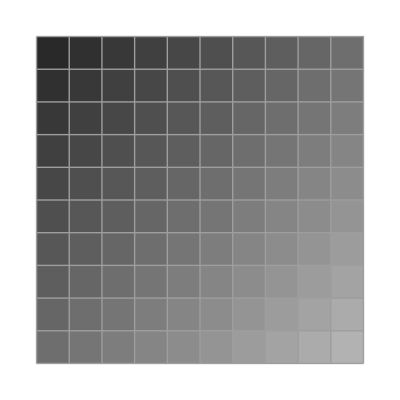

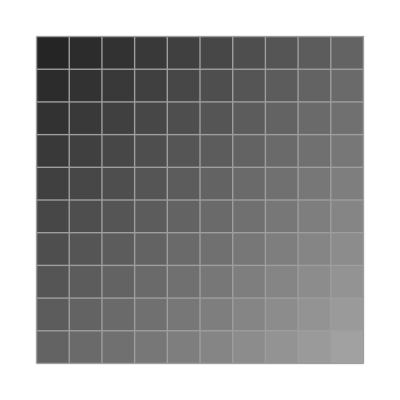

```mathematica
test1=Table[0.1+0.03*i+0.03*j,{i,1,10},{j,1,10}];
test2=test1*0.9;
ArrayPlot[test1,ColorFunction->(Blend[{Black,White},#]&),PlotRange->{0,1},Mesh->True]
ArrayPlot[test2,ColorFunction->(Blend[{Black,White},#]&),PlotRange->{0,1},Mesh->True]
```

```mathematica
ArrayPlot[bgrid[[-1]]]
```

(0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851)